Applying Wolfram model transformations to Wolfram model rules

```mathematica
wm = ResourceFunction["WolframModel"]
```

```mathematica
rule = ResourceFunction["RandomWolframModel"][{{2,2}}->{{4,2}}]
```

{{1,2},{2,3}}→{{2,1},{2,4},{5,2},{3,1}}

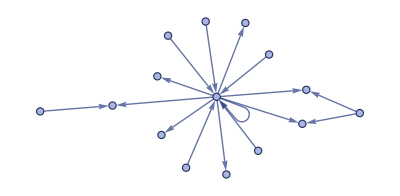

```mathematica
wm[rule, Automatic, 3, "FinalStatePlot"]
```

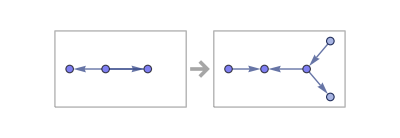

```mathematica
RulePlot[wm[rule]]
```

```mathematica
wm[rule, Automatic, 2, "FinalState"]
```

{{1,1},{1,4},{5,1},{2,1},{1,3},{1,6},{7,1},{1,3}}

```mathematica
rule = ResourceFunction["CanonicalWolframModelRule"][{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}}]
```

{{1,2},{1,3}}→{{1,2},{1,4},{2,4},{3,4}}

```mathematica
DirectedGraph[rule[[1]]]
```

-Graphics-

```mathematica
DirectedGraph[rule[[2]]]
```

-Graphics-

```mathematica
RulePlot[wm[rule]]
```

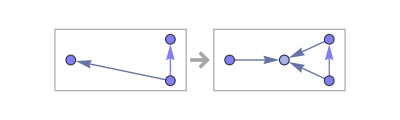

```mathematica
ruleForm = Apply[Rule, rule, {2}]
```

{1→2,1→3}→{1→2,1→4,2→4,3→4}

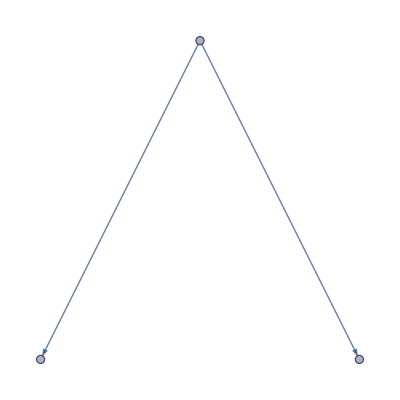

```mathematica
g = Graph[ruleForm[[1]]]
```

```mathematica
EdgeList@g
```

{1->2,1->3}

```mathematica
VertexList@g
```

{1,2,3}

## Mutate single graph

```mathematica
addRandomConnection[g_] := EdgeAdd[g, Rule @@ RandomChoice[VertexList @ g, 2]]
addRandomEdge[g_] := EdgeAdd[g, Rule[RandomChoice[VertexList @ g], VertexCount[g] + 1]]
```

```mathematica
deleteRandomEdge[g_] := EdgeDelete[g, RandomChoice[EdgeList @ g]]
deleteRandomVertex[g_] := VertexDelete[g, RandomChoice[VertexList @ g]]
```

```mathematica
g
```

-Graphics-

```mathematica
VertexList@g
```

{1,2,3}

```mathematica
EdgeList@g
```

{1->2,1->3}

```mathematica
modifyRandomElement[g_] := 
reverseRandomEdge
```

```mathematica
operations = {addRandomConnection, addRandomEdge, deleteRandomEdge, deleteRandomVertex};
mutate[g_] := RandomChoice[operations] @ g
```

```mathematica
mutate[g]
```

-Graphics-

## Mutate single WM rule

```mathematica
rule
```

{{1,2},{1,3}}→{{1,2},{1,4},{2,4},{3,4}}